```mathematica
Solve[f^2(1+δ^2/l1^2)+(g^2 l1^2)/4==f(v0^2+g δ),f]
```

{{f→(v0^2+g δ-√(-g^2 l1^2+v0^4+2 g v0^2 δ))/(2 (1+δ^2/l1^2))},{f→(v0^2+g δ+√(-g^2 l1^2+v0^4+2 g v0^2 δ))/(2 (1+δ^2/l1^2))}}

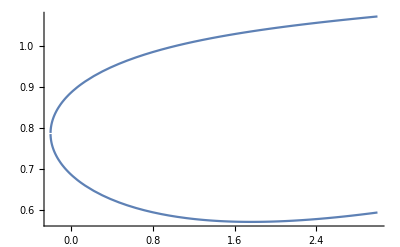

```mathematica
Plot[{ArcTan[√((2(v0^2+2g δ)(1+δ^2/l1^2))/(v0^2+2g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))-1)],ArcTan[√((2(v0^2+2g δ)(1+δ^2/l1^2))/(v0^2+2g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))-1)]}/.v0->10/.g->9.8/.l1->10,{δ,-1,3},PlotRange->All]
```

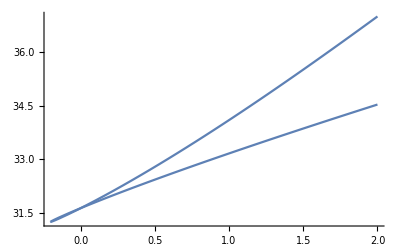

```mathematica
Plot[{√(H^2+(l2+δ+2/g √((v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2),√(H^2+(l2+δ+2/g √((v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2)}/.H->10/.l1->10/.l2->20/.g->9.8/.v0->10,{δ,-1,2},PlotRange->All]
```

```mathematica
√(10^2+22^2)//N
```

24.1661

```mathematica
NMaximize[{√(H^2+(l2+δ+2/g √((v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2)/.H->10/.l1->10/.l2->20/.g->9.8/.v0->10,0<δ<2},δ]
```

{37.0126,{δ→2.}}

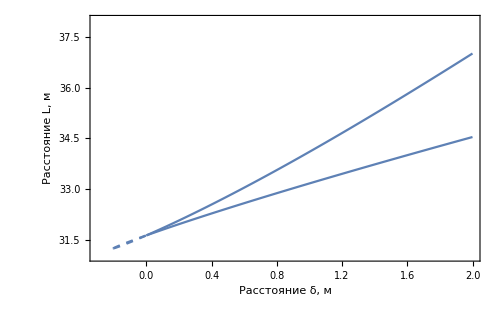

```mathematica
Show[Plot[{√(H^2+(l2+δ+2/g √((v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2),√(H^2+(l2+δ+2/g √((v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2)}/.H->10/.l1->10/.l2->20/.g->9.8/.v0->10,{δ,0,2},PlotRange->{{-0.3,2},{31,38}},Axes->False,
Frame->True,FrameTicks->{{Automatic,False},{Automatic,False}},ImageSize->500,FrameTicksStyle->Directive[FontFamily->"Times New Roman",20],FrameLabel->{Style["Расстояние δ, м",20,FontFamily->"Times New Roman"],Style["Расстояние L, м",20,FontFamily->"Times New Roman"]}],Plot[{√(H^2+(l2+δ+2/g √((v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ+√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2),√(H^2+(l2+δ+2/g √((v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2)))√(v0^2+2g δ-(v0^2+g δ-√(v0^4+2 v0^2 g δ-g^2 l1^2))/(2(1+δ^2/l1^2))))^2)}/.H->10/.l1->10/.l2->20/.g->9.8/.v0->10,{δ,-0.5,0},PlotStyle->Dashed]]
```

```mathematica
D[Cos[x](Sin[x]+√(a^2+Sin[x]^2)),x]
```

Cos[x] (Cos[x]+(Cos[x] Sin[x])/(√(a^2+Sin[x]^2)))-Sin[x] (Sin[x]+√(a^2+Sin[x]^2))

```mathematica
Solve[%1==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ArcCos[-(√(1+a^2))/(√(2+a^2))]},{x→ArcCos[-(√(1+a^2))/(√(2+a^2))]},{x→-ArcCos[(√(1+a^2))/(√(2+a^2))]},{x→ArcCos[(√(1+a^2))/(√(2+a^2))]}}

```mathematica
Cos[x](Sin[x]+√(a^2+Sin[x]^2))/.%2[[4]]//FullSimplify
```

√(1-1/(2+a^2)) (√(1/(2+a^2))+√(a^2+1/(2+a^2)))

```mathematica
FullSimplify[%5,a>0]
```

√(1+a^2)

```mathematica
%5/.a->0
```

1

```mathematica
(v √(v^2+2g h))/g/.v->10/.g->9.8/.h->10
```

17.5558